Iteration: 0

Max. norm: 3.29566

Second norm of the residual: 6.88252

Iteration: 1

Max. norm: 6.19309

Second norm of the residual: 9.21531+2.77089 ⅈ

Iteration: 2

Max. norm: 2.16891

Second norm of the residual: 4.44201+1.09636 ⅈ

Iteration: 3

Max. norm: 0.222678

Second norm of the residual: 0.102927+0.60265 ⅈ

Iteration: 4

Max. norm: 0.00231859

Second norm of the residual: 0.00603983-0.00279011 ⅈ

Iteration: 5

Max. norm: 2.76134×10^-7

Second norm of the residual: 5.12204×10^-7-6.0404×10^-7 ⅈ

Iteration: 6

Max. norm: 3.85674×10^-15

Second norm of the residual: 2.69734×10^-15+1.08901×10^-14 ⅈ

Soltion of SLAE (6.08244+0. ⅈ
5.52897+0. ⅈ
5.11039-7.88861×10^-31 ⅈ
4.82955-2.36658×10^-30 ⅈ
4.68857+7.88861×10^-31 ⅈ
4.68857+1.57772×10^-30 ⅈ
4.82955-7.88861×10^-31 ⅈ
5.11039+0. ⅈ
5.52897+0. ⅈ
6.08244+1.57772×10^-30 ⅈ)

Time required on the solution 0.7488603

Comparison f[t] with Numeric solution 1. | 1.00004
0.669421 | 0.669455
0.404959 | 0.405017
0.206612 | 0.20668
0.0743802 | 0.0744498
0.00826446 | 0.00832376
0.00826446 | 0.00832376
0.0743802 | 0.0744498
0.206612 | 0.20668
0.404959 | 0.405017
0.669421 | 0.669455
1. | 1.00004

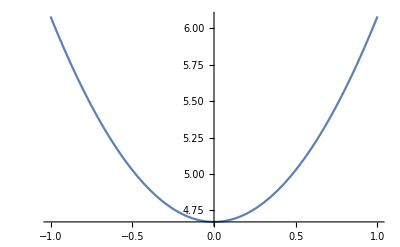

```mathematica
StartTime=AbsoluteTime[];
(*==============================*)
(* Functions and params defentions *)
(*==============================*)

(* Left boundary*)
a=-1;
(* Right boundary*)
b=1;
(*Accurancy of Newton's method*)
eps=10^(-12);
(*Maximum steps for Newton's method*)
MAXITER=30;
(*Kernel*)
K[ξ_,t_,u_]=Sqrt[ξ^2+t^2+u];
(*Rhs function*)
f[t_]=t^2;
DD [ξ_,t_,u_]= D[K[ξ,t,u],u];
(* Number on nodes *)
NN = 10;
(*Grid*)
UniformGrid = Table[i,{i,a,b,(b-a)/(NN-1)}]; 
ff=f[UniformGrid];


(*=======================================*)
(*Filling universal vector α for integrating*)
(*========================================*)
α=Table[0,{NN}];
For[j=1, j<=NN, j++,
(*Preparation for the natural spline making*)
w=Table[{UniformGrid[[i]],0.0},{i,1,NN}]; (*Pairs of values {grid point, function values}*)
w[[j,2]]=1; (*Definition of natural spline as a spline through only 1 nodes with value 1 and others are 0*)(*Interpolation polynom*)
S=Interpolation[w];
α[[j]]=Integrate[S[x], {x,a,b}];
]


(*===============================*)
(*========Newton's Algorythm========*)
(*===============================*)

(*Initial condition for solution*)
λ=Table[0.0,{NN}];
(*Counter for iterations*)
kk=0;

SNorm=1;
(*Newton's algorythm*)
While[SNorm>=eps,
(*Left hand side matrix assemble*)
Lhs=Table[If[i!=j,
-α[[j]]*DD[UniformGrid[[j]],UniformGrid[[i]],λ[[j]]],
1-α[[j]]*DD[UniformGrid[[j]],UniformGrid[[i]],λ[[j]]]
],{i,1,NN},{j,1,NN}];
(*Right hand side assemble*)
Rhs=Table[ff[[i]]-λ[[i]]+Sum[α[[j]]*K[UniformGrid[[j]],UniformGrid[[i]],λ[[j]]],{j,1,NN}],{i,1,NN}];

(*Find additivies*)
NodesSolution=LinearSolve[Lhs,Rhs];
(*New solution vector*)
λ=λ+NodesSolution;
SNorm=Max[Abs[Rhs]];
Print["Iteration: ", kk];
Print["Max. norm: ", SNorm];
Print["Second norm of the residual: ", Sqrt[Rhs.Rhs]];
kk++;
If[kk>=MAXITER,Break[]; Print["Maximum iterations required"]];
];
(*======================================*)
(*========End of Newton's Algorythm=======*)
(*=====================================*)


If[Length[λ]<=20,Print["Soltion of SLAE ", MatrixForm[λ]]]; 
CalculationTime=AbsoluteTime[];
Print["Time required on the solution ", CalculationTime-StartTime];

(*=====================*)
(*Solution visualisation*)
(*=====================*)
SolutionInterpolation=Interpolation[Table[{UniformGrid[[i]],λ[[i]]},{i,1,NN}]];
SolutionAccuracyCheck=Table[{f[t]//N, SolutionInterpolation[t]-NIntegrate[K[x,t,SolutionInterpolation[x]],{x,a,b}]}, {t,a,b,(b-a)/11}];
Print["Comparison f[t] with Numeric solution ", SolutionAccuracyCheck //TableForm];
Plot[SolutionInterpolation[x],{x,a,b},PlotRange->All]
Print["Required time to solve the problem ", AbsoluteTime[]-StartTime];
```